# MATH7501 Practical 11 (Week 12), Semester 1-2021

## Topic: Probability Distributions

Author:  Aminath Shausan
Date: 21-05-2021

# Pre-Tutorial Activity

Students must have familiarised themselves with units 9 and 10 contents  of the reading materials for MATH7501

# Resources

Chapters 9 and 10: Computation of mean, variance, expectation, gradient decent method

https://en.wikipedia.org/wiki/Rayleigh_distribution

# Section 1: The Rayleigh Distribution

In probability theory and statistics,the Rayleigh distribution is a continuous probability distribution for nonnegative-valued random variables.

The notation X~Rayleigh(σ) means that the random variable X has a Rayleigh distribution with shape parameter σ.The probability density function  (pdf) is:

```mathematica
Subscript[f, X](x)= {{{x/σ^2 e^(-x^2/(2 σ^2))  ,    x ≥0, σ>0}, {0,                              x <0}}
```

```mathematica
Q1) Plot the pdf of X for σ = 0.5, 1, 2, 3
```

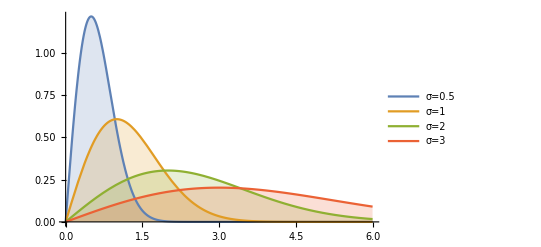

```mathematica
Plot[Table[PDF[RayleighDistribution[σ],x],{σ,{.5,1,2,3}}]//Evaluate,
{x,0,6},Filling->Axis,PlotRange->All, PlotLegends->{"σ=0.5", "σ=1", "σ=2", "σ=3"}]
```

```mathematica
Q2) Show that the cumulative distribution function (cdf) of X is 
                   Subscript[F, X](x)= {{{1-e^(-x^2/(2 σ^2))  , x ≥0}, {0,             x <0}}
```

```mathematica
Subscript[F, X](x) = P(X≤x)  = ∫_0^x Subscript[f, X](t)dt
                                      = ∫_0^x t/σ^2 e^(-t^2/(2 σ^2))dt 
Let u = (t^2/(2 σ^2)). Then du = t/σ^2 dt, and the limits of the integral are u=0 and u = (x^2/(2 σ^2)). Thus, substituting dt = σ^2/t du in the above integration, we have, 

Subscript[F, X](x) =∫_0^(x^2/(2 σ^2)) e^-u du 
             =-[e^-u ]_(u=0)^(u=x^2/(2 σ^2))
             =-{e^(-x^2/(2 σ^2))-e^0}
             ={{{1-e^(-x^2/(2 σ^2)) , x ≥0}, {0,             x <0,}}
```

```mathematica
as required.
```

```mathematica
You can also use the Integrate[] function to compute the cdf as shown below.
```

```mathematica
f[x_]:=x/σ^2 E^(-x^2/(2 σ^2))(*Rayleigh probability density function*)
```

```mathematica
Integrate[f[x],{x,0,u}] (*cdf*)
```

1-ⅇ^(-u^2/(2 σ^2))

```mathematica
Q3) Show that Subscript[f, X](x) is a valid probability density function by showing that the integral over [0, ∞) is 1
```

```mathematica
Method 1: Show this using calculus
 ∫_0^∞ Subscript[f, X](t)dt = ∫_0^∞ x/σ^2 e^(-x^2/(2 σ^2))dx
                        =Subscript[limit, y->∞]∫_0^y x/σ^2 e^(-x^2/(2 σ^2))dx
                        =Subscript[limit, y->∞] Subscript[F, x](y), by the definition of the cdf
                        =Subscript[limit, y->∞](1-e^(-x^2/(2 σ^2)))
                        = 1-0
                        =1, as required.
```

```mathematica
Method 2: Use the Integrate[] function to compute this integration exactly in Mathematica.
```

```mathematica
Integrate[f[x],{x,0,∞}, Assumptions -> σ>0]
```

1

```mathematica
Method 3: You can also use NIntegrate[] function to derive a numerical approximation to ∫_0^∞ x/σ^2 e^(-x^2/(2 σ^2))dx,for a given value of σ (say for example, σ=1).
```

```mathematica
NIntegrate[x E^(-x^2/2), {x,0,∞}]
```

1.

```mathematica
Method 4: Approximate the integral by Reiman sum
(*discretisation sum *)
```

```mathematica
Clear[δ] (*δ is the width of the rectangle*)
```

```mathematica
Total[Table[ x E^(-x^2/2)δ,{x,0,10000,δ=0.01}]]
```

0.999992

```mathematica
Q4) Show that  the mean of X ~ Rayleigh(σ) = σ√π/2
```

```mathematica
Subscript[μ, X] = E(X)  = ∫_0^∞ Subscript[xf, X](x)dx
                         = ∫_0^∞ x x/σ^2 e^(-x^2/(2 σ^2))dx
Let u = (x^2/(2 σ^2)). Then du = x/σ^2 dx, and the limits of the integral are still  u=0 and u=∞. Thus, substituting dx = σ^2/x du  and using x =√(2 σ^2 u) in the above integration we have,
```

```mathematica
Subscript[μ, X] = ∫_0^∞ √(2 σ^2 u)e^-u du
          =σ √2∫_0^∞ √u e^-u du
          = σ √2∫_0^∞ u^(3/2 -1)e^-u du
          = σ √2Γ(3/2), Γ(x) is the Gamma function defined as: Γ(x) =∫_0^∞ t^(x -1)e^-t dt
          = σ √2 Γ(1/2+1)
          = σ √2  1/2 Γ(1/2), using the property of Gamma function, Γ(x+1) =xΓ(x)
          =σ √2  1/2 √π ,  using the property of Gamma function, Γ(1/2) =√π
    =σ √(π/2)
```

```mathematica
You can use the Integrate[] function to check your derivation of  the mean as follows.
```

```mathematica
Integrate[x f[x],{x,0,∞}, Assumptions -> σ>0]  (*mean (μ) *)
```

√(π/2) σ

```mathematica
(*using numerical approximation to compute the mean when σ =1*)
```

```mathematica
NIntegrate[x  x E^(-x^2/2),{x,0,∞}]
```

1.25331

```mathematica
δ = 0.01
```

0.01

```mathematica
Total[Table[x  x E^(-x^2/2)δ,{x,0,10,δ}]]
```

1.25331

```mathematica
Q5)Show that the variance of X~ Rayleigh(σ) = σ^2((4-π)/2)
From Week 11 prctical, we know that Subscript[σ^2, X]=var(X) = E[X^2]-Subscript[μ, X]^2, where E[X^2] is the second moment of X and Subscript[μ, X] is the mean of X, which we computed in Q4. Thus, it remains to find an expression for E[X^2] . We will require the integration bi-parts formula ∫u dv = uv -∫v du for this calculation. 
E[X^2] = ∫_(-∞)^∞ x^2 Subscript[f, X](x)dx
              = ∫_0^∞ x^2 x/σ^2 e^(-x^2/(2 σ^2))dx
                     = [x^2 ∫_0^∞ x/σ^2 e^(-x^2/(2 σ^2))dx]_(x=0)^(x=∞)- ∫_0^∞ 2x(∫_0^∞ x/σ^2 e^(-x^2/(2 σ^2))dx)dx, by using u = x^2  and  dv = x/σ^2 e^(-x^2/(2 σ^2)),
                    = [-x^2 e^(-x^2/(2 σ^2))]_(x=0)^(x=∞) + ∫_0^∞ 2x e^(-x^2/(2 σ^2))dx
To evaluate the integral, let u = (x^2/(2 σ^2)). Then du = x/σ^2 dx, and the limits of the integral are still  u=0 and u=∞. Thus, substituting dx = σ^2/x du  we have
                   E[X^2]= 0 +2(σ^2)[∫_0^∞ e^-u du]
                              =-2 Subscript[(σ^2)[e^-u], u=0]^(u=∞) 
                              = -2(σ^2)[0 - 1]
                              = 2 σ^2
Thus, Subscript[σ^2, X]=var(X) = E[X^2]-Subscript[μ, X]^2
                                        =2 σ^2 - (σ √(π/2) )^2
                                        =σ^2((4-π)/2) as required.
```

```mathematica
You can use the Integrate[] function to check your work.
```

```mathematica
Integrate[x^2 f[x],{x,0,∞}, Assumptions -> σ>0] (*compute second moment (E[X^2]*)
```

2 σ^2

```mathematica
(*using numerical approximation to compute the second moment when σ =1*)
```

```mathematica
NIntegrate[x^2 x E^(-x^2/2),{x,0,∞}]
```

2.

```mathematica
Total[Table[x^2 x E^(-x^2/2)δ,{x,0,10,δ}]]
```

2.

```mathematica
(*variance*)
E[X^2]- μ^2 = 2 σ^2 -(√(π/2) σ)^2
```

2 σ^2-(π σ^2)/2

```mathematica
Q6)Find the median of X.
```

```mathematica
Note that the median of X is the number M such that, 
                             ∫_0^M Subscript[f, X](x)dx = 1/2
Note that the left hand side is the cdf of X evaluated at M. Thus we have
```

```mathematica
Subscript[F, X](M) = 1/2
                           1-e^(-M^2/(2 σ^2))= 1/2
                                 e^(-M^2/(2 σ^2))= 1/2
                               - M^2/(2 σ^2)= ln(1/2)
                                  M^2= -2 σ^2 ln(1/2)
                                 M=σ √(-2ln(1/2)) as the median.
```

```mathematica
Q7) The quantile function of the distribution,q(u) for u∈[0,1),is defined as follows:For each u,we should have,
                               ∫_0^(q(u)) Subscript[f, X](x)dx = u
```

```mathematica
a) Find an expression for q(u)
```

```mathematica
By noting that the left-hand side of the equation is the cdf of X evaluated at q(u), we have
```

```mathematica
Subscript[F, X](q(u)) = u
                           1-e^(-(q(u)^2)/(2 σ^2))= u
                                 e^(-(q(u)^2)/(2 σ^2))= 1-u
                               - (q(u)^2)/(2 σ^2)= ln(1-u)
                                  q(u)^2= -2 σ^2 ln(1-u) 
    q(u)= σ√(-2ln(1-u))
```

```mathematica
b)Say that X = q(U) with  U  as Uniformly distributed on [0,1]. Then, X has a Rayleigh distribution. Show this empirically for σ=1,  by generating 10^4 uniform random variables on [0,1]
```

```mathematica
(*Generate a Rayleigh random Variable from Uniform[0,1] random variable*)
```

```mathematica
U =RandomReal[1,10000];
X=Sqrt[-2Log[1-U]];
```

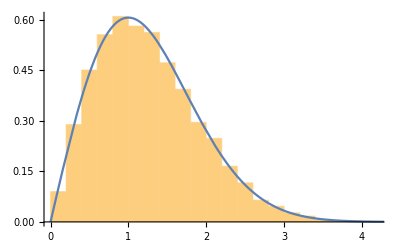

```mathematica
Show[Histogram[X,Automatic, "PDF"],
Plot[PDF[RayleighDistribution[1],x],
{x,0,8}, PlotRange->All]]
```

```mathematica
The plot shows histogram of the data X along with the pdf of X~RayleighDistribution(1).
```

# Section 2: Simple Linear Regression Problem

Consider the simple linear regression problem  with data points  (x_1,y_1), ..., (x_n, y_n). The aim is to seek β_0 and β_1 to fit the line,
                                                    y = β_0 + β_1x,
 by minimizing the loss function
                                                L(β_0 β_1) = ∑_(i=1)^n (y_i-(β_0+β_1 x_i))^2 .
  Here, β_0 and β_1 are the slope and the intercept, respectively, of the line of best fit.

Q1) Compute an expression for the gradient of L(β_0 β_1)

```mathematica
Since the loss function has two variables, we need to use partial derivatives here. 
((∂L(Subscript[β, 0] Subscript[β, 1]))/(∂Subscript[β, 1]))= ∂/(∂Subscript[β, 1])∑_(i=1)^n (Subscript[y, i]-(Subscript[β, 0]+Subscript[β, 1] Subscript[x, i]))^2 
                              = ∑_(i=1)^n ∂/(∂Subscript[β, 1])(Subscript[y, i]-(Subscript[β, 0]+Subscript[β, 1] Subscript[x, i]))^2 
                              = (-2∑)_(i=1)^n Subscript[x, i](Subscript[y, i]-(Subscript[β, 0]+Subscript[β, 1] Subscript[x, i]))

 (∂L(Subscript[β, 0] Subscript[β, 1]))/(∂Subscript[β, 0])= ∂/(∂Subscript[β, 0])∑_(i=1)^n (Subscript[y, i]-(Subscript[β, 0]+Subscript[β, 1] Subscript[x, i]))^2 
                              = ∑_(i=1)^n ∂/(∂Subscript[β, 0])(Subscript[y, i]-(Subscript[β, 0]+Subscript[β, 1] Subscript[x, i]))^2 
                              = (-2∑)_(i=1)^n(Subscript[y, i]-(Subscript[β, 0]+Subscript[β, 1] Subscript[x, i]))
```